```mathematica
Manipulate[DiscretePlot[Minimize[{c, 
  CDF[BinomialDistribution[n, p], c] >= 95/100 && 
   0 < c <= 200}, c, Integers][[1]], {p, 1/40, 1/5, 1/40}, PlotRange->{0, 50}], {n, 50, 250, 10}]
```

```mathematica
DiscretePlot[Minimize[{c, 
  CDF[BinomialDistribution[208, 1/20], c] >= 95/100 && 
   0 < c <= 50}, c, Integers], {n, 1, 50}]
```

```mathematica
Show[DiscretePlot[CDF[BinomialDistribution[208, 1/20], x],  {x, 0, 50}, PlotStyle->Red], DiscretePlot[CDF[BinomialDistribution[30, 1/20], x],  {x, 0, 50}]]
```

So I have one email blast with n = 30 and one email blast with n = 208. My question is what would I need to see to show with 95% confidence that the probability of the 208 is higher

```mathematica
DiscretePlot[CDF[BinomialDistribution[30, 1/20], 5], {x, 1, 50}, PlotRange->All]
```

```mathematica
N[CDF[BinomialDistribution[208, 1/20], 10]]
```

```mathematica
N[CDF[BinomialDistribution[30, 1/20], 3]]
```

```mathematica
N[53656302244465014980697931384222328551/53687091200000000000000000000000000000]
```

```mathematica
Manipulate[DiscretePlot[CDF[BinomialDistribution[n, p], x],  {x, 0, 10}, PlotStyle->Red, PlotRange->{0, 1}],{n, 0, 50, 5}, {p, 0, 0.2, 0.001}]
```

```mathematica
ResourceFunction["DarkMode"][]
```

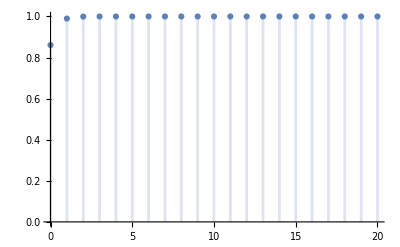
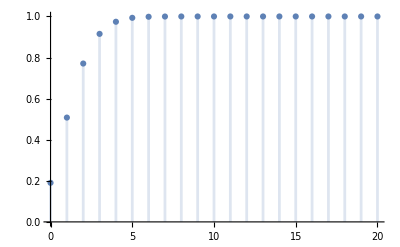
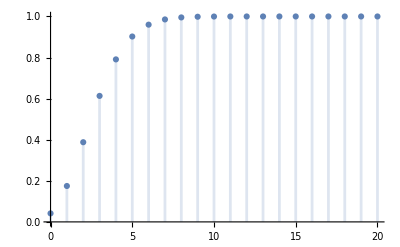
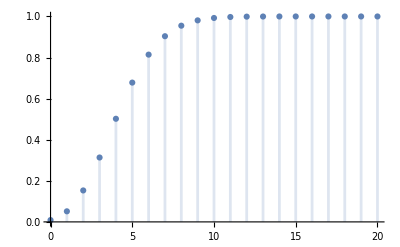
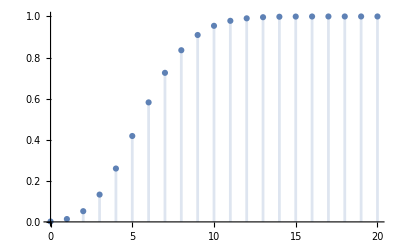
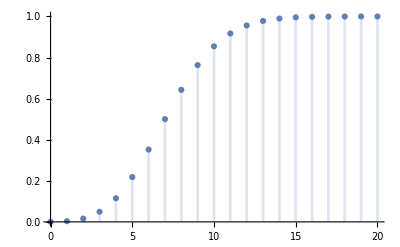
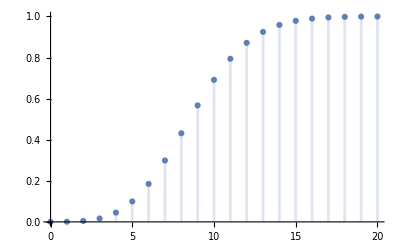
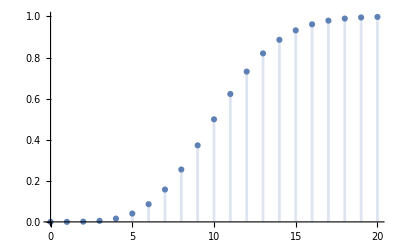

```mathematica
Table[
DiscretePlot[CDF[BinomialDistribution[150, p], x],  {x, 0, 20}, PlotRange->{0,1}],
 {p, 1/1000, 1/10, 1/100}]
```